```mathematica
SetDirectory[NotebookDirectory[]];
```

## Import data & format

```mathematica
populationRaw = Import["population by latitude and longitude, 2000.csv"];
```

```mathematica
landRaw = Import["land by latitude and longitude.csv"];
```

From: https://eosweb.larc.nasa.gov/cgi-bin/sse/global.cgi?email=skip@larc.nasa.gov

```mathematica
sunshine = Association[ #⟦{1,2}⟧->#⟦3⟧&/@Import["global_radiation.txt", "Table"]⟦15;;, {1,2, 15}⟧ ];
```

```mathematica
land = Thread[Tuples[{#⟦2;;,1⟧, #⟦1,2;;⟧}]-> Flatten[#⟦2;;,2;;⟧]]&@landRaw⟦9;;,3;;⟧;
landLowRes = Total[#⟦All,2⟧]&/@GroupBy[ land, {Floor[#⟦1,1⟧],Floor[#⟦1,2⟧]} &] ;
```

```mathematica
population = Thread[Tuples[{#⟦2;;,1⟧, #⟦1,2;;⟧}]-> Flatten[#⟦2;;,2;;⟧]]&@populationRaw⟦2;;,2;;⟧;
populationLowRes = Total[#⟦All,2⟧]&/@GroupBy[ population, {Floor[#⟦1,1⟧],Floor[#⟦1,2⟧]} &] ;
```

```mathematica
MinMax/@Transpose@(landLowRes//Keys )
```

{{-90,89},{-180,179}}

## Population density estimates

```mathematica
landLat = Transpose@{landRaw⟦10;;, 3⟧, landRaw⟦10;;, 2⟧};
populationLat = Transpose@{populationRaw⟦3;;, 2⟧, populationRaw⟦3;;, 1⟧};
```

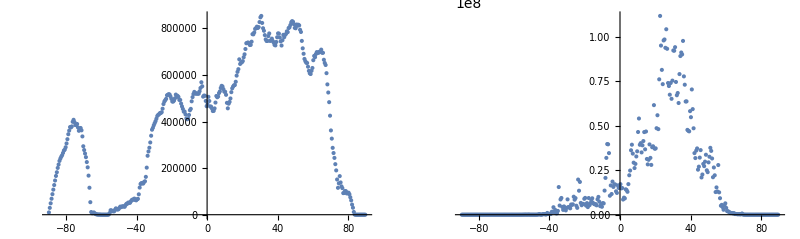

```mathematica
{ListPlot[ landLat], ListPlot[ populationLat]}//GraphicsRow
```

```mathematica
landLon = Transpose@{landRaw⟦9, 4;;⟧, landRaw⟦8, 4;;⟧};
populationLon = Transpose@{populationRaw⟦2, 3;;⟧, populationRaw⟦1, 3;;⟧};
```

```mathematica
normalizedPopulationLat = Transpose@{populationLat⟦All, 1⟧,  populationLat⟦All, 2⟧/landLat⟦All, 2⟧} /.{Indeterminate -> 0.0};
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

## Sunshine estimates

Remove water area since we can use it

```mathematica
landQ= #>0&/@landLowRes;
sunshineLand = KeySort@KeySelect[sunshine, landQ];
```

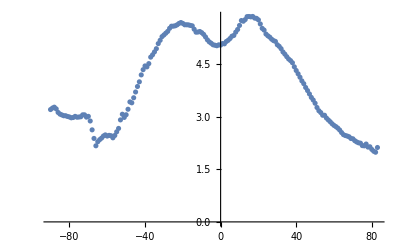

```mathematica
sunshineMeanLat =Mean[#⟦All,2⟧]&/@GroupBy[ Normal@sunshineLand , #⟦1,1⟧ &];
sunshineMeanLat // ListPlot
```

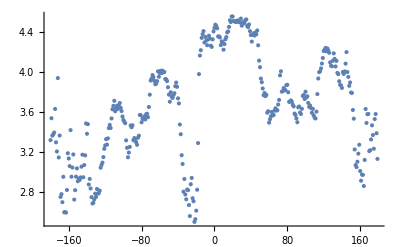

```mathematica
sunshineMeanLon =Mean[#⟦All,2⟧]&/@GroupBy[ Normal@sunshineLand , #⟦1,2⟧ &];
sunshineMeanLon // ListPlot
```

```mathematica
normalizedPopulationLon = Transpose@{populationLon⟦All, 1⟧,  populationLon⟦All, 2⟧/landLon⟦All, 2⟧} /.{Indeterminate -> 0.0};
```

## Lon / Lat plots

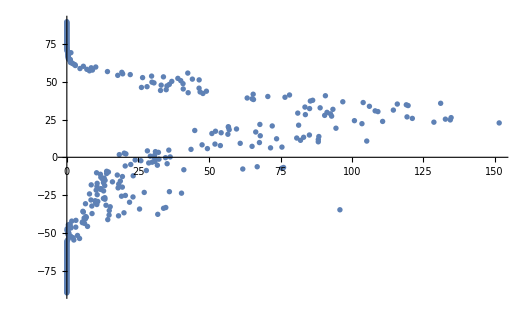

```mathematica
ListPlot[Reverse[normalizedPopulationLat,2]]
```

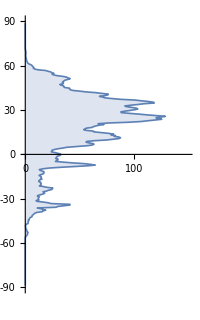

```mathematica
smoothNormPopLat = Transpose@{
MovingAverage[ normalizedPopulationLat⟦All, 1⟧, 5],
MovingAverage[ normalizedPopulationLat⟦All, 2⟧, 5]
};

fig1 =ListPlot[Reverse[smoothNormPopLat,2], Joined->True, Filling->Axis, AspectRatio->1.6, Ticks-> {{0, 50, 100, 150}, Range[-90, 90, 30]},
PlotRange->{{0,150}, {-90,90}}, 
ImageSize-> 200,
AxesStyle->Directive[FontSize-> 11],
PlotStyle->AbsoluteThickness[1.2]
]
```

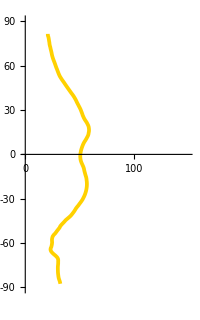

```mathematica
smoothSunshineLat = SortBy[Transpose@{
MovingAverage[ Normal[sunshineMeanLat]⟦All, 1⟧, 5]+0.5,
MovingAverage[ Normal[sunshineMeanLat]⟦All, 2⟧, 5]*10
}, First];

fig2 =ListPlot[Reverse[smoothSunshineLat,2], Joined->True, AspectRatio->1.6, Ticks-> {{0, 50, 100, 150}, Range[-90, 90, 30]},
PlotRange->{{0,150}, {-90,90}}, 
ImageSize-> 200,
PlotStyle->Directive[RGBColor[1.,0.82,0.],AbsoluteThickness[2.7]],
AxesStyle->Directive[FontSize-> 11],
AxesOrigin-> {0,0}
]
```

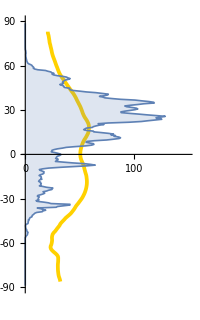

```mathematica
fig = Show[fig2, fig1]
```

```mathematica
Export[ "/Users/kmisiunas/Documents/Curiosities/World population distribution/fig_latitude_distribution.pdf", fig]
```

/Users/kmisiunas/Documents/Curiosities/World population distribution/fig_latitude_distribution.pdf

```mathematica
smoothNormPopLon = Transpose@{
MovingAverage[ normalizedPopulationLon⟦All, 1⟧, 5],
MovingAverage[ normalizedPopulationLon⟦All, 2⟧, 5]
};
```

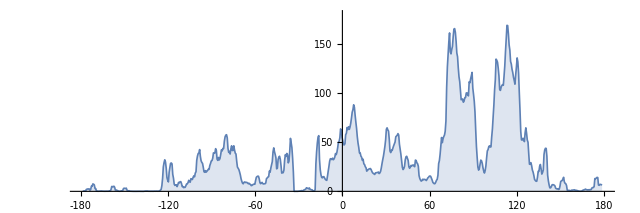

```mathematica
fig1 = ListPlot[ smoothNormPopLon, Joined->True, Filling->Axis,
Ticks-> {Range[-180, 180, 30],{0, 50, 100, 150}},
PlotRange->{{-180,180}, {0,180}},
ImageSize-> 200*1.6*2, AspectRatio->1/3,
AxesStyle->Directive[FontSize-> 11],
PlotStyle->AbsoluteThickness[1.2]
]
```

```mathematica
smoothSunshineLon = Transpose@{
MovingAverage[Normal[ sunshineMeanLon]⟦All, 1⟧, 5]+0.5,
MovingAverage[ Normal[sunshineMeanLon]⟦All, 2⟧, 5]*15
};
```

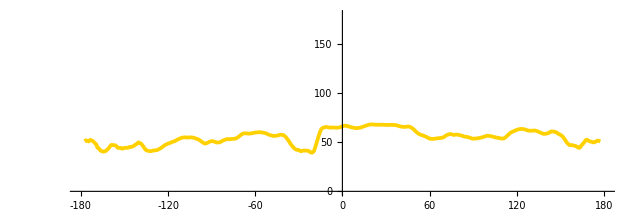

```mathematica
fig2 = ListPlot[ smoothSunshineLon, Joined->True, 
Ticks-> {Range[-180, 180, 30],{0, 50, 100, 150}},
PlotRange->{{-180,180}, {0,180}},
PlotStyle->Directive[RGBColor[1.,0.82,0.],AbsoluteThickness[2.7]],
ImageSize-> 200*1.6*2, AspectRatio->1/3,
AxesStyle->Directive[FontSize-> 11],
PlotStyle->AbsoluteThickness[1.2]
]
```

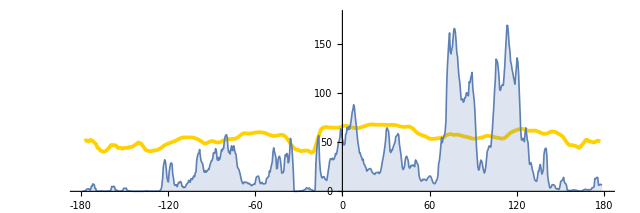

```mathematica
fig = Show[fig2, fig1]
```

```mathematica
Export[ "/Users/kmisiunas/Documents/Curiosities/World population distribution/fig_longitude_distribution.pdf", fig]
```

## Map plot

/Users/kmisiunas/Documents/Curiosities/World population distribution/fig_longitude_distribution.pdf

```mathematica
data= GeoPosition[#⟦1⟧+{0.5,0.5}] -> #⟦2⟧&/@Normal[sunshineLand];
```

```mathematica
GeoRegionValuePlot[RandomSample[data, 1000],GeoBackground->GeoStyling["ReliefMap"]]
```

```mathematica
data//Flatten // Length
```

25532

```mathematica
Polygon[EntityClass["Country","LandMasses"]]
```

```mathematica
area[pos_]:= Polygon[  GeoPosition /@ {pos, pos + {1,0}, pos +{1,1}, pos+{0,1}, pos}];
```

```mathematica
area[pos_]:= GeoPosition [ {pos, pos + {1,0}, pos +{1,1}, pos+{0,1}, pos}];
```

```mathematica
area[pos_]:= Rectangle@GeoPosition [ pos];
```

```mathematica
allWater=Polygon[GeoPosition[Join@@((EntityValue[EntityClass["Ocean", All],"Polygon"]/.{Missing -> Nothing})/.Polygon[GeoPosition[x_]]:>x)]];
```

```mathematica
GeoListDensityPlot[data_]:= Module[
{colorRange, colorRegion, color},
colorRange = MinMax[data];
color = ColorData["Rainbow"];
colorRegion[pos_ -> value_]:={ color[(value-colorRange⟦1⟧)/(colorRange⟦2⟧-colorRange⟦1⟧)], area[pos]};
GeoGraphics[{
colorRegion/@Normal[data],
GeoStyling["ReliefMap"], allWater
} , GeoBackground->GeoStyling["Coastlines"] ]
]
```

```mathematica
fig = GeoListDensityPlot[ sunshineLand  ]
```

#### Compute relevant metrics

```mathematica
sunshine//Length
```

64800

```mathematica
populationLowRes//Length
```

64800

```mathematica
landLowRes//Length
```

64800

```mathematica
sunshine
```

```mathematica
populationDencityLand = KeySort@KeySelect[ KeySort@populationLowRes/KeySort@landLowRes, landQ];
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
populationDencityLand⟦;;10⟧
```

<|{-90,-180}→0,{-90,-179}→0,{-90,-178}→0,{-90,-177}→0,{-90,-176}→0,{-90,-175}→0,{-90,-174}→0,{-90,-173}→0,{-90,-172}→0,{-90,-171}→0|>

```mathematica
sunshineLand⟦;;10⟧
```

<|{-90,-180}→3.19,{-90,-179}→3.19,{-90,-178}→3.19,{-90,-177}→3.19,{-90,-176}→3.19,{-90,-175}→3.19,{-90,-174}→3.19,{-90,-173}→3.19,{-90,-172}→3.19,{-90,-171}→3.19|>

```mathematica
sunshineLand//Mean
```

3.82315

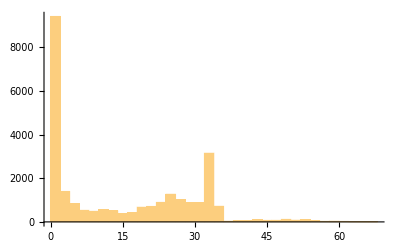

```mathematica
data = sunshineLand/(populationDencityLand +0.1);
data// Histogram
```

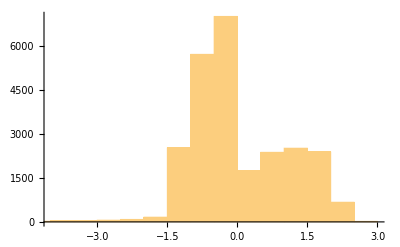

```mathematica
Standardize[Values@sunshineLand]  // Histogram
```

```mathematica
-Standardize[Values@populationDencityLand]
```

{-0.194143,-0.194143,-0.194143,-0.194143,-0.194143,-0.194143,-0.194143,-0.194143,-0.194143,25515,-0.194133,-0.194132,-0.194133,-0.194135,-0.194134,-0.19413,-0.19413,-0.194137}
 |  |  |  |

```mathematica
data = Association@Thread[Keys[sunshineLand]-> (Standardize[Values@sunshineLand] - Standardize[Values@populationDencityLand])];
data// Histogram
```

-Graphics-

```mathematica
baund[x_] := Max[Min[x, 2], -2]
```

```mathematica
fig = GeoListDensityPlot[ baund/@data  ]
```

-Graphics-

```mathematica
Export[ "fig_map.png", fig, ImageSize -> 1000, ImageResolution-> 1000]
```

fig_map.png